```mathematica
data1=Import[NotebookDirectory[]<>"..\\..\\data\\2020_Problem_D_DATA\\passingevents.csv"];
```

```mathematica
object=Transpose[data1][[{1,2,6}]];
```

```mathematica
myteam=Drop[Thread[Table[object[[i]],{i,1,3}]],1];
```

```mathematica
Flexibility[match_]:={
allteamfnmatch1=Cases[myteam1,{match,_,_}];
allteamfn1match1=Drop[#,1]&/@allteamfnmatch1;
sequence1=Flatten@Position[#[[1]]&/@allteamfn1match1,"Huskies"];
a=Split[sequence1,#2-#1==1&];
listnew={};
For[i=1,i<Length[a],i++,listnew=Append[Append[listnew,Identity@@Take[a[[i]],-1]],Identity@@Take[a[[i+1]],1]]];
index=Partition[listnew,2,2];
time=#[[2]]&/@allteamfn1match1;
timeline=(time[[#[[2]]]]-time[[#[[1]]]])&/@index
}
```

```mathematica
Flexibility[1];
```

```mathematica
sequence1
```

{1,3,5,6,9,11,12,14,18,19,20,22,24,26,31,33,34,39,40,41,43,45,46,47,49,51,52,53,55,57,59,61,63,64,65,66,67,68,69,71,72,73,74,75,76,77,80,83,84,86,87,88,90,91,93,95,96,97,98,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,130,131,132,133,134,135,136,137,138,139,140,141,150,152,154,161,163,166,168,169,172,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,197,198,199,200,202,203,205,208,209,210,211,212,216,218,219,221,224,225,226,228,229,234,237,238,239,240,242,244,246,247,248,253,254,255,258,260,261,262,264,266,270,273,274,287,289,291,299,300,304,305,306,307,308,309,310,311,312,314,315,316,317,319,320,321,322,325,327,328,329,330,331,332,335,338,340,342,343,345,350,352,353,354,355,356,357,360,361,362,363,364,365,366,367,368,369,370,372,374,375,376,377,378,379,380,381,382,383,384,385,386,387,388,389,390,391,392,393,394,395,397,399,400,402,403,406,408,409,411,412,413,415,416,417,419,422,424,425,426,427,429,431,432,433,434,435,436,437,438,439,440,441,442,445,447,448,449,450,451,452,455,456,458,460,463,465,466,467,468,469,470,471,472,473,474,475,476,480,481,482,484,486,487,488,489,490,499,500,501,502,503,504,505,506,507,508,509,510,511,512,513,514,515,516,517,518,519,520,522,523,524,525,528,530,532,535,538,541,542,546,548,550,552,553,558,562,564,565,566,567,568,569,570,572,574,576,577,579,580,586,587,588,589,590,591,592,593,594,597,601,602,603,604,605,607,608,610,613,614,615,616,617,618,619,620,621,622,624,625,631,632,634,635,636,637,643,645,646,647,648,649,650,652,653,654,656,658,659,665,666,668,670,672,676,678,680,682,683,685,688,690,694,695,696,697,698,699,702,707,709,712,713,715,716,717,718,719,720,721,722,724,725,726,728,736,737,738,742,745,748,749,750,751,753,754,755,756,757,758,759,760,761,763,764,765,766,767,770,771,773,777,780,783,784,785,786,787,788,789,790,791,794,798,802,804,807,808,809,810,811,813,815,816,818,821,822,825,827,829,830,832,835,836,838,839,840,843,848,849,850,854,857,860,861,862,863,864,866,867,869,873,874,876,877,879,880,881,884,885,886,889,891,892,893,894,896,897,898,900,901,902,903,904,905,906,907,908,910,914,918,920,921,928,929,931,933,935,939,941,944,946,947,948,950,952,954,955,957,960,962,963,965,967,969,973,975,976,979,980,981,982,983,985,989,990,991,993,994,995,996,997,999,1000,1001,1005,1007,1009,1010,1011,1012,1013,1014,1016,1017,1018,1020,1021,1022,1025,1026,1029,1031,1032,1034,1035,1036,1037,1039,1040,1041,1042,1043,1046,1047,1048,1049,1050,1051,1052,1053,1054,1055,1056,1057,1058,1059,1060,1061,1062,1063,1064,1066,1067,1068,1070,1071,1072,1074,1075,1078,1080,1081,1084,1085,1087,1088,1089,1090,1091,1092,1093,1099,1101,1104,1106,1110,1111,1113,1114,1115,1116,1117,1119,1120,1121,1122,1123,1124,1127,1128,1129,1130,1131,1132,1133,1134,1137,1138,1139,1140,1144,1146,1148,1150,1152,1154,1155,1157,1159,1161,1162,1163,1166,1171,1172,1173,1176,1178,1181,1184,1186,1187,1191,1192,1193,1194,1195,1197,1198,1200,1201,1202,1203,1204,1212,1214,1216,1218,1219,1220,1221,1223,1231,1233,1236,1237,1238,1239,1241,1243,1244,1245,1248,1251,1254,1255,1260,1262,1263,1264,1265,1267,1275,1277,1279,1281,1285,1286,1290,1293,1296,1299,1302,1304,1305,1306,1308,1310,1311,1312,1314,1315,1316,1322,1325,1329,1330,1332,1338,1340,1341,1343,1348,1355,1357,1360,1365,1367,1368,1372,1374,1376,1377,1378,1379,1381,1383,1384,1389,1392,1393,1396,1398,1400,1401,1402,1403,1404,1405,1406,1407,1408,1409,1410,1413,1414,1417,1418,1419,1421,1423,1425,1426,1427,1428,1430,1431,1434,1437,1438,1440,1442,1444,1446,1447,1450,1452,1454,1457,1459,1461,1463,1465,1467,1470,1474,1477,1480,1481,1482,1483,1485,1486,1490,1492,1494,1495,1496,1498,1499,1500,1501,1503,1508,1510,1512,1514,1516,1518,1520}

```mathematica
index
```

{{1,3},{3,5},{6,9},{9,11},{12,14},{14,18},{20,22},{22,24},{24,26},{26,31},{31,33},{34,39},{41,43},{43,45},{47,49},{49,51},{53,55},{55,57},{57,59},{59,61},{61,63},{69,71},{77,80},{80,83},{84,86},{88,90},{91,93},{93,95},{98,104},{120,130},{141,150},{150,152},{152,154},{154,161},{161,163},{163,166},{166,168},{169,172},{172,174},{191,197},{200,202},{203,205},{205,208},{212,216},{216,218},{219,221},{221,224},{226,228},{229,234},{234,237},{240,242},{242,244},{244,246},{248,253},{255,258},{258,260},{262,264},{264,266},{266,270},{270,273},{274,287},{287,289},{289,291},{291,299},{300,304},{312,314},{317,319},{322,325},{325,327},{332,335},{335,338},{338,340},{340,342},{343,345},{345,350},{350,352},{357,360},{370,372},{372,374},{395,397},{397,399},{400,402},{403,406},{406,408},{409,411},{413,415},{417,419},{419,422},{422,424},{427,429},{429,431},{442,445},{445,447},{452,455},{456,458},{458,460},{460,463},{463,465},{476,480},{482,484},{484,486},{490,499},{520,522},{525,528},{528,530},{530,532},{532,535},{535,538},{538,541},{542,546},{546,548},{548,550},{550,552},{553,558},{558,562},{562,564},{570,572},{572,574},{574,576},{577,579},{580,586},{594,597},{597,601},{605,607},{608,610},{610,613},{622,624},{625,631},{632,634},{637,643},{643,645},{650,652},{654,656},{656,658},{659,665},{666,668},{668,670},{670,672},{672,676},{676,678},{678,680},{680,682},{683,685},{685,688},{688,690},{690,694},{699,702},{702,707},{707,709},{709,712},{713,715},{722,724},{726,728},{728,736},{738,742},{742,745},{745,748},{751,753},{761,763},{767,770},{771,773},{773,777},{777,780},{780,783},{791,794},{794,798},{798,802},{802,804},{804,807},{811,813},{813,815},{816,818},{818,821},{822,825},{825,827},{827,829},{830,832},{832,835},{836,838},{840,843},{843,848},{850,854},{854,857},{857,860},{864,866},{867,869},{869,873},{874,876},{877,879},{881,884},{886,889},{889,891},{894,896},{898,900},{908,910},{910,914},{914,918},{918,920},{921,928},{929,931},{931,933},{933,935},{935,939},{939,941},{941,944},{944,946},{948,950},{950,952},{952,954},{955,957},{957,960},{960,962},{963,965},{965,967},{967,969},{969,973},{973,975},{976,979},{983,985},{985,989},{991,993},{997,999},{1001,1005},{1005,1007},{1007,1009},{1014,1016},{1018,1020},{1022,1025},{1026,1029},{1029,1031},{1032,1034},{1037,1039},{1043,1046},{1064,1066},{1068,1070},{1072,1074},{1075,1078},{1078,1080},{1081,1084},{1085,1087},{1093,1099},{1099,1101},{1101,1104},{1104,1106},{1106,1110},{1111,1113},{1117,1119},{1124,1127},{1134,1137},{1140,1144},{1144,1146},{1146,1148},{1148,1150},{1150,1152},{1152,1154},{1155,1157},{1157,1159},{1159,1161},{1163,1166},{1166,1171},{1173,1176},{1176,1178},{1178,1181},{1181,1184},{1184,1186},{1187,1191},{1195,1197},{1198,1200},{1204,1212},{1212,1214},{1214,1216},{1216,1218},{1221,1223},{1223,1231},{1231,1233},{1233,1236},{1239,1241},{1241,1243},{1245,1248},{1248,1251},{1251,1254},{1255,1260},{1260,1262},{1265,1267},{1267,1275},{1275,1277},{1277,1279},{1279,1281},{1281,1285},{1286,1290},{1290,1293},{1293,1296},{1296,1299},{1299,1302},{1302,1304},{1306,1308},{1308,1310},{1312,1314},{1316,1322},{1322,1325},{1325,1329},{1330,1332},{1332,1338},{1338,1340},{1341,1343},{1343,1348},{1348,1355},{1355,1357},{1357,1360},{1360,1365},{1365,1367},{1368,1372},{1372,1374},{1374,1376},{1379,1381},{1381,1383},{1384,1389},{1389,1392},{1393,1396},{1396,1398},{1398,1400},{1410,1413},{1414,1417},{1419,1421},{1421,1423},{1423,1425},{1428,1430},{1431,1434},{1434,1437},{1438,1440},{1440,1442},{1442,1444},{1444,1446},{1447,1450},{1450,1452},{1452,1454},{1454,1457},{1457,1459},{1459,1461},{1461,1463},{1463,1465},{1465,1467},{1467,1470},{1470,1474},{1474,1477},{1477,1480},{1483,1485},{1486,1490},{1490,1492},{1492,1494},{1496,1498},{1501,1503},{1503,1508},{1508,1510},{1510,1512},{1512,1514},{1514,1516},{1516,1518},{1518,1520}}

```mathematica
timeline//Total
```

1369.53

```mathematica
timeline//Length
```

359

```mathematica
Table[Length[Flatten[Flexibility[c]]]/Total[Flatten[Flexibility[c]]],{c,1,38}]
```

{0.262134,0.178854,0.200558,0.0794223,0.214886,0.0800036,0.262024,0.219276,0.16317,0.259703,0.0749132,0.191942,0.17204,0.225638,0.0757229,0.138583,0.0755891,0.192096,0.178481,0.194468,0.0927641,0.193377,0.224307,0.286035,0.171923,0.215115,0.205313,0.217039,0.0848534,0.205788,0.0743771,0.106672,0.199839,0.209443,0.0905634,0.198689,0.0772949,0.169224}

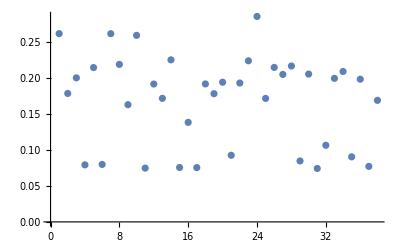

```mathematica
ListPlot[%1965]
```

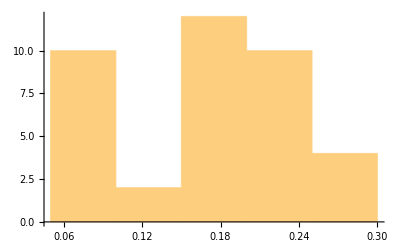

```mathematica
Histogram[%1907]
```

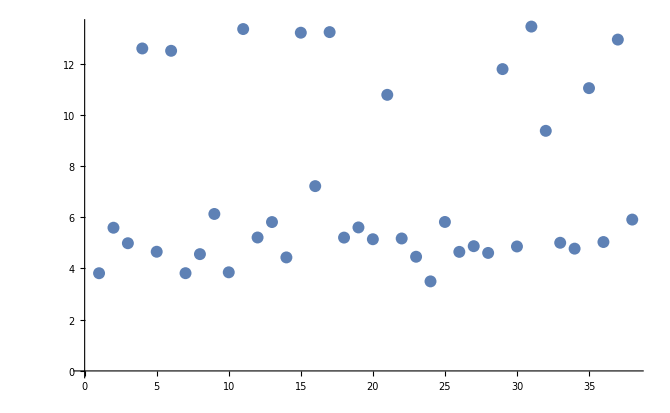

```mathematica
ListPlot[%1887]
```

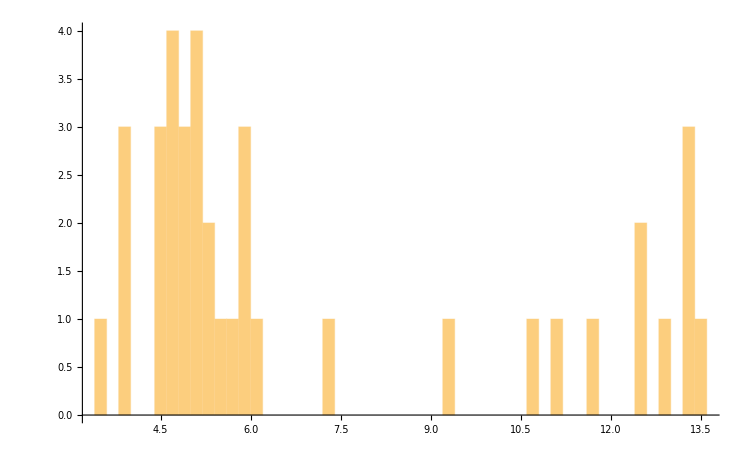

```mathematica
Histogram[%1887,38]
```

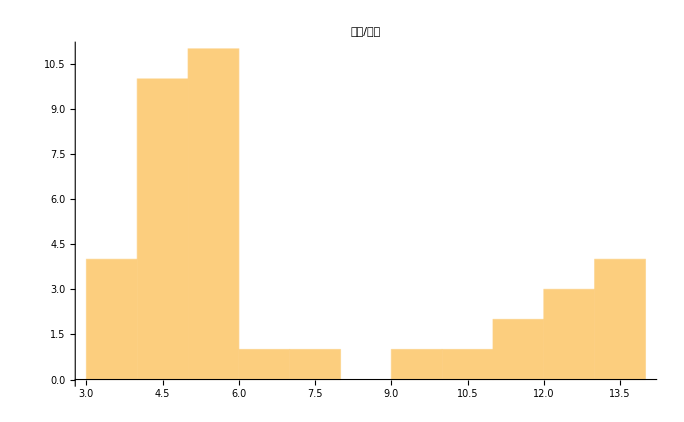

```mathematica
Show[%1892,PlotLabel->HoldForm[次数/时间],LabelStyle->{GrayLevel[0]}]
```

```mathematica
Total@Flatten@Flexibility[1]/Length@Flatten@Flexibility[1]
```

3.81484

```mathematica
Total@Flatten@Flexibility[2]/Length@Flatten@Flexibility[2]
```

5.59116

```mathematica
Total@Flatten@Flexibility[1]
```

1369.53

```mathematica
Length@Flatten@Flexibility[1]
```

359

```mathematica
1369.5265959999992/359
```

3.81484

```mathematica
Flexibility[1]//Flatten//Total
```

1369.53

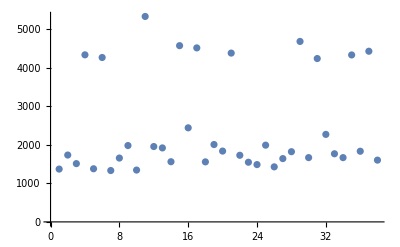

```mathematica
ListPlot[%1862]
```

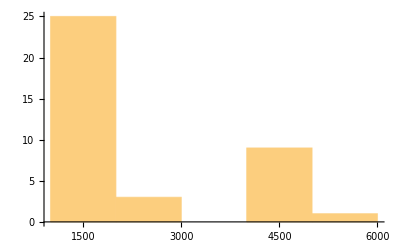

```mathematica
Histogram[%1862]
```

```mathematica
listnew[[1;;20]]
```

{1,3,3,5,6,9,9,11,12,14,14,18,20,22,22,24,24,26,26,31}

```mathematica
{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}//Length
```

38

```mathematica
allteamfnmatch1=Cases[myteam1,{1,_,_}];
allteamfn1match1=Drop[#,1]&/@allteamfnmatch1;
sequence1=Flatten@Position[#[[1]]&/@allteamfn1match1,"Huskies"];
```